## Curing derivative kick (Prob. 3.7)

basic idea is to differentiate the measured signal but not the reference, in the feedback loop “D term”

```mathematica
Clear["Global`*"];
```

UnitStep[t]

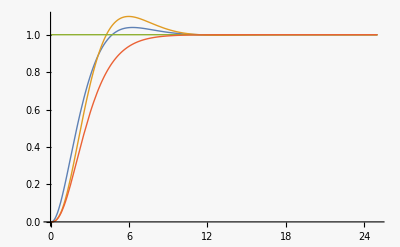

```mathematica
tmax=25; sys=1/(1+ s)^3;k0=1/s;kpi=kp+ki/s; kpid=kpi+(kd s)/(1+tf s);
pars={kp->1,ki->0.5,kd->0.5,tf->0.1};
(* u=UnitStep[t-1] + UnitStep[t-11] does not work -- a Mathematica bug? *)
u=UnitStep[t]
G0=TransferFunctionModel[sys,s];
y0=OutputResponse[G0/.pars,u,{t,0,tmax}]; (* open loop step response *)
sys1=(sys kpid)/(1+sys kpid);sys2=(sys kpi)/(1+sys kpid);
G1=TransferFunctionModel[sys1,s]//Simplify; (* closed loop PID step resp *)
y1=OutputResponse[G1/.pars,u,{t,0,tmax}];
G2=TransferFunctionModel[sys2,s]//Simplify;  (* no derivative kick *)
y2=OutputResponse[G2/.pars,u,{t,0,tmax}];
Plot[{y1,y2,u,y0},{t,0,tmax},PlotRange->All]
```

notice that y1step is more aggressive than y2 (it uses the derivative kick to “get going”).

Now look at controller output

```mathematica
sys1u=kpid/(1+sys kpid);sys2u=kpi/(1+sys kpid);
```

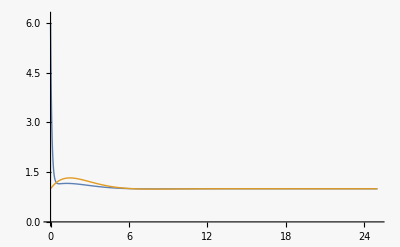

```mathematica
u1tf=TransferFunctionModel[sys1u,s]//FullSimplify; (* closed loop PID input *)
u1=OutputResponse[u1tf/.pars,u,{t,0,tmax}];
u2tf=TransferFunctionModel[sys2u,s]//FullSimplify;  (* no derivative kick *)
u2=OutputResponse[u2tf/.pars//Simplify,u,{t,0,tmax}];
Plot[{u1,u2},{t,0,tmax},PlotRange->{0,6.2}]
```

But the big difference here is that eliminating the derivative kick makes the output much less “spiky”, which 
can be an advantage.  For example, if the output controls a mechanical component (relay, piezoelectric element, etc.) they do not like to be “slammed”.

Export data.

```mathematica
dt=0.01;
dat = Table[{y0[[1]],y1[[1]],y2[[1]],u1[[1]],u2[[1]]},{t,0,tmax,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["derivativeKick.dat", dat];
*)
```